Определяне на интервалите на изпъкналост и вдлъбналост на дункцията, и инфлексните точки

```mathematica
f[x_]:=уравнение;
Solve[D[f[x], x,x]==0]
```

{{x→0},{x→-√3},{x→√3}}

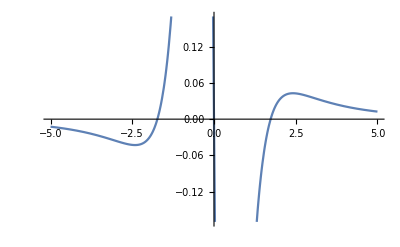

```mathematica
Plot[f''[x],{x, -5, 5}, AxesOrigin->{0, 0}]
```

```mathematica
f1=f'[x];
f2=f''[x];
f3=f'''[x];
```

```mathematica
Solve[f2==0, x]
```

{{x→0},{x→-√3},{x→√3}}

```mathematica
x1=0;
x2=-√3;
x3=√3;
```

```mathematica
If[((f2/.x->x1)==0)&&((f3/.x->x1)≠0), Print["Има инфлексна точка с координати: (", x1, ",", f[x1], ")"], Print["Тази точка не е инфлексна!"]]
```

Има инфлексна точка с координати: (0,0)

```mathematica
If[((f2/.x->x2)==0)&&((f3/.x->x2)≠0), Print["Има инфлексна точка с координати: (", x2, ",", f[x2], ")"], Print["Тази точка не е инфлексна!"]]
```

Има инфлексна точка с координати: (-√3,-(√3)/4)

```mathematica
If[((f2/.x->x3)==0)&&((f3/.x->x3)≠0), Print["Има инфлексна точка с координати: (", x3, ",", f[x3], ")"], Print["Тази точка не е инфлексна!"]]
```

Има инфлексна точка с координати: (√3,(√3)/4)

```mathematica
Print["Изпъкналост при: ", Reduce[f2>0, x]];
Print["Вдлъбнатост при: ", Reduce[f2<0, x]];
```

Изпъкналост при: -√3<x<0||x>√3

Вдлъбнатост при: x<-√3||0<x<√3

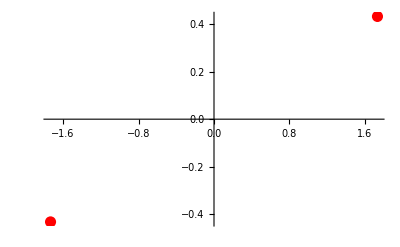

```mathematica
Plot[f[x], {x, -2, 2.4}, Epilog->{Red, PointSize[.02], Point[{-√3, -(√3)/4}], Point[{√3,(√3)/4}]}]
```